```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<Data`;
```

```mathematica
data=nxrData[-1];
ff=Freq23[];
Dimensions[data]
```

{50,2,6,46}

```mathematica
(*check which distribution the data is*)
```

```mathematica
pd=Flatten[data[[All,All,1,{3,4}]],{{1,2},{3}}];
Dimensions[%]
```

{100,2}

```mathematica
H=DistributionFitTest[pd[[All,1]],Automatic,"HypothesisTestData"]
```

HypothesisTestData[«DistributionFitTest»]

```mathematica
t=H["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 22.3447 | 0.
Cramér-von Mises | 4.22892 | 0.
Jarque-Bera ALM | 35419.1 | 0.
Kolmogorov-Smirnov | 0.336041 | 0.
Kuiper | 0.639142 | 3.16477×10^-17
Pearson χ^2 | 100. | 5.4497×10^-17
Shapiro-Wilk | 0.23175 | 1.69096×10^-20
Watson U^2 | 4.14786 | 0.

```mathematica
(*Export["aa.emf",t]*)
```

aa.emf

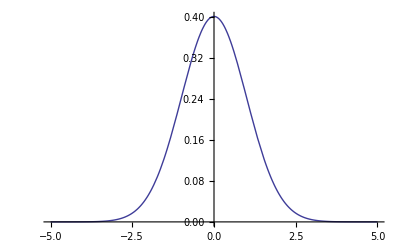

```mathematica
Plot[PDF[H["FittedDistribution"],x],{x,-5,5}]
```

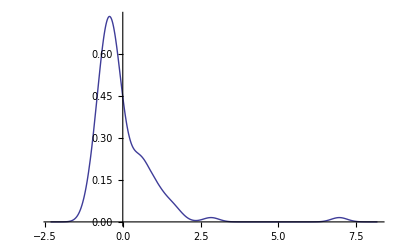

-3.02015×10^-17

```mathematica
SmoothHistogram[pd[[All,1]]]
(*Mean[pd[[All,2]]]*)
(* is this a Gaussian dist?*)
```

```mathematica
pd[[All,1]];
```

```mathematica
fdata=Flatten[data,{{1,2},{3,4}}];
```

```mathematica
cv=Covariance[fdata];
```

```mathematica
cv[[1]]
```

{1.,-0.633109,0.854411,-0.0580165,0.701741,0.0230573,0.476844,0.0901511,0.379778,0.108,0.28411,0.134707,0.059412,0.16023,0.045914,0.176026,0.0179153,0.173145,-0.00479791,0.18275,-0.0185846,0.19191,-0.0181121,0.195568,-0.043445,0.214784,-0.0536079,0.226379,-0.0811015,0.241198,-0.10015,0.235263,-0.098454,0.256037,-0.104598,0.266772,-0.111736,0.27695,-0.112959,0.295586,-0.117254,0.309604,-0.120502,0.326243,-0.102172,0.361574,0.182519,0.0132621,0.18982,0.069147,0.182955,0.105951,0.182521,0.127714,0.181507,0.13863,0.176443,0.143775,0.174336,0.144955,0.172963,0.141942,0.17115,0.14281,0.17024,0.143572,0.169087,0.144233,0.168503,0.141824,0.167501,0.143228,0.16683,0.142443,0.164964,0.142863,0.165955,0.142992,0.164844,0.142848,0.165346,0.142547,0.164491,0.143904,0.163983,0.132669,0.163373,0.142569,0.165085,0.132308,0.161065,0.14225,0.169959,-0.00593846,0.176842,0.0325171,0.176676,0.0782459,0.131743,0.0333768,0.177926,0.115154,0.175281,0.122526,0.17432,0.125489,0.172939,0.122403,0.170433,0.125934,0.170502,0.127364,0.170668,0.129777,0.170255,0.128262,0.169498,0.130345,0.171964,0.123895,0.168728,0.128375,0.169175,0.128132,0.168756,0.130233,0.167285,0.130063,0.167007,0.129663,0.166556,0.137076,0.166522,0.132597,0.165419,0.134435,0.162605,0.130508,0.15698,0.0516056,0.16533,0.0750027,0.163246,0.0912305,0.156609,0.113864,0.15319,0.12336,0.152175,0.12214,0.150675,0.120781,0.149295,0.118759,0.149791,0.121619,0.148936,0.122798,0.148982,0.121137,0.1493,0.121429,0.147804,0.123435,0.147047,0.124587,0.146748,0.118935,0.147808,0.12139,0.146734,0.122563,0.145996,0.122136,0.146172,0.121163,0.141525,0.130657,0.141727,0.118499,0.143857,0.125131,0.14118,0.0982733,0.156978,0.0141601,0.163853,0.0557327,0.163291,0.077743,0.162223,0.0973961,0.159657,0.111201,0.159481,0.11114,0.158362,0.111066,0.156586,0.107653,0.158162,0.110295,0.15783,0.110882,0.157524,0.110663,0.15607,0.113578,0.155453,0.113155,0.154484,0.114162,0.154153,0.11056,0.154202,0.115401,0.154458,0.111042,0.1539,0.108236,0.152143,0.109991,0.153812,0.118802,0.153316,0.117259,0.147495,0.11406,0.14951,0.116401,0.142922,-0.0232082,0.150338,0.0208652,0.152189,0.0463893,0.146514,0.0740182,0.143276,0.0891573,0.14275,0.0910468,0.14219,0.0915355,0.142096,0.0876716,0.140942,0.092405,0.140708,0.0924164,0.141114,0.096304,0.141181,0.091133,0.139456,0.0888739,0.140268,0.0891522,0.138568,0.0889079,0.139169,0.0900594,0.137895,0.0891133,0.137637,0.0909581,0.139461,0.090849,0.137716,0.0953698,0.140025,0.0897374,0.136225,0.0947862,0.134925,0.088228}